## Poincare

```mathematica
Let K be a field and suppose that an elliptic curve E is given by an equation of the form
E: y^2=x^3+A x+B with A,B∈K.
Let E(K) denote the set of points of E with coordinates in K,
E(K)={(x,y)∈E: x,y∈K}∪{𝒪}.
Then E(K) is a subgroup of the group of all points of E.
```

```mathematica
EllipticQ[x_,y_,A_,B_,m_]:=Mod[y^2-(x^3+A x+B),m];
```

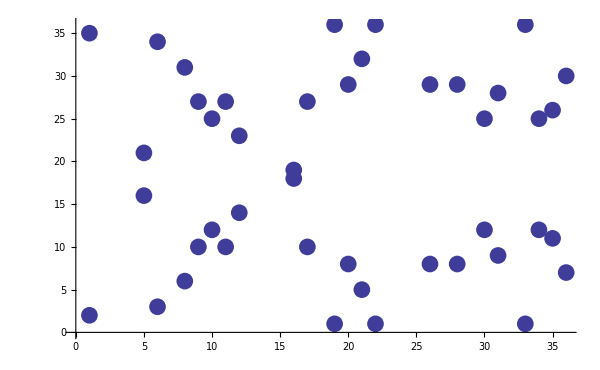

```mathematica
m=37;
A=-5;
B=8;
EllipticPoints=Select[Flatten[Table[{i,j},{i,m},{j,m}],1],EllipticQ[#[[1]],#[[2]],A,B,m]==0&];
ListPlot[EllipticPoints,PlotStyle->PointSize[0.02],ImageSize->{600,400}]
```

## Theorem

```mathematica
Working over a finite field, the group of points E(Subscript[𝔽, p]) is always either a cyclic group or the product of two cyclic groups.
```

```mathematica
WeierstrassP[u,{Subscript[g, 2],Subscript[g, 3]}]=x ⟺ ∫_∞^x 1/(√(4 t^3-Subscript[g, 2] t-Subscript[g, 3]))ⅆt=u
```

```mathematica
℘(z)=1/z^2+∑_((ω∈L)_(ω≠0)) (1/(z-ω)^2-1/ω^2)
```

```mathematica
℘(z+ω)=℘(z) for all ω∈L.
```

```mathematica
E(ℂ)≅𝕔/L≅S^1×S^1
```

```mathematica
E Subscript[(𝕔), N]={P∈E(𝕔): N P=𝒪} for any integer N≥1
```

```mathematica
E Subscript[(𝕔), N]≅Subscript[C, N]×Subscript[C, N] for all N≥1
```

## Mordell

```mathematica
Let E be an elliptic curve given by an equation
E:y^2=x^3+A x+B with A,B∈ℚ.
Then the group of rational points E(ℚ) is a finitely generated abelian group. 
In other words, there is a finite set of points Subscript[P, 1], ..., Subscript[P, t]∈E(ℚ) 
so that every point P∈E(ℚ) can be written in the form
P=Subscript[n, 1] Subscript[P, 1]+Subscript[n, 2] Subscript[P, 2]+...+Subscript[n, t] Subscript[P, t] for some Subscript[n, 1], Subscript[n, 2], ..., Subscript[n, t]∈ℤ.
```

## Siegel

## Hasse

## Birch